Zad. 1

```mathematica
Integrate[x^3/Sqrt[x^4+1],x]//FullSimplify
Integrate[x^4 Log[x],x]
```

(√(1+x^4))/2

-x^5/25+1/5 x^5 Log[x]

Zad. 2

```mathematica
Series[x^(1/3),{x,1,2}]//Normal
%/.{x->1.1}
1.1^(1/3)
```

1+1/3 (-1+x)-1/9 (-1+x)^2

1.03222

1.03228

Zad. 3

```mathematica
(x+2)(x^2-2)//Expand;
Integrate[%,x]12//Expand
%//TeXForm
```

-48 x-12 x^2+8 x^3+3 x^4

3 x^4+8 x^3-12 x^2-48 x

Zad. 4           
f(x) = x^3, 0<=x<=3

Zad.5

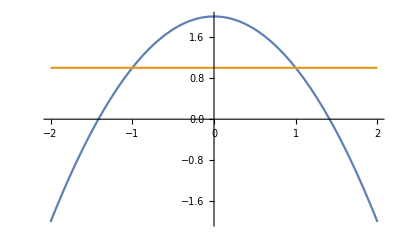

4/3

```mathematica
y1=4-x^2;
y2=3;
Plot[{y1,y2},{x,-2,2}]
Integrate[y1-y2,{x,-1,1}]
```

Zad. 6

```mathematica
Log[2x +3x y-y^2];
D[%,y]
D[%,x]//Simplify
```

(3 x-2 y)/(2 x+3 x y-y^2)

(y (4+3 y))/((y^2-x (2+3 y))^2)